## Roy Smart Oral Comp 2017 Explaining the Talbot Effect

```mathematica
Clear["Global`*"]
```

## Solving the Fresnel diffraction integral

#### The Kirchhoff diffraction integrand is given as

```mathematica
ψ = ψ0/(2 I λ)q[X] Exp[I k s0]/s0 Exp[I k s]/s(Cos[θ0]+Cos[θ1]);
```

#### where we define the coordinates

```mathematica
s0 = √((x0-X)^2+(y0-Y)^2+z0^2);
s = √((x - X)^2+(y-Y)^2+z^2);
```

#### and we are assuming

```mathematica
$Assumptions = λ > 0 && k > 0 && x0 ∈ Reals && y0 ∈ Reals && z0∈Reals && x ∈ Reals && y ∈ Reals && z ∈ Reals && n ∈ Integers && a > 0
```

λ>0&&k>0&&x0∈Reals&&y0∈Reals&&z0∈Reals&&x∈Reals&&y∈Reals&&z∈Reals&&n∈Integers&&a>0

#### Assuming the aperture is much smaller than the path length (xi-X)^2+(yi-Y)^2<< zi, we may use the small angle approximation

```mathematica
s0 = Series[s0,{z0,Infinity,1}] //Normal
s = Series[s,{z,Infinity,1}] //Normal
```

(X^2-2 X x0+x0^2+Y^2-2 Y y0+y0^2)/(2 z0)+z0

(x^2-2 x X+X^2+y^2-2 y Y+Y^2)/(2 z)+z

#### Under this approximation, we also take the small angle approximation on the cosine terms

```mathematica
θ0 = θ1 = 0;
```

#### Define the transmission function

```mathematica
q[x_] := An Exp[(2 I π n x)/a]
```

#### Using the above approximations, the Kirchhoff integrand becomes the Fresnel diffraction integrand.

```mathematica
ψ
```

-(ⅈ An ⅇ^((2 ⅈ n π X)/a+ⅈ k ((x^2-2 x X+X^2+y^2-2 y Y+Y^2)/(2 z)+z)+ⅈ k ((X^2-2 X x0+x0^2+Y^2-2 Y y0+y0^2)/(2 z0)+z0)) ψ0)/(((x^2-2 x X+X^2+y^2-2 y Y+Y^2)/(2 z)+z) ((X^2-2 X x0+x0^2+Y^2-2 Y y0+y0^2)/(2 z0)+z0) λ)

#### Keep only second-order terms in the denominator

```mathematica
ψ
```

-(ⅈ An ⅇ^((2 ⅈ n π X)/a+ⅈ k ((x^2-2 x X+X^2+y^2-2 y Y+Y^2)/(2 z)+z)+ⅈ k ((X^2-2 X x0+x0^2+Y^2-2 Y y0+y0^2)/(2 z0)+z0)) ψ0)/(((x^2-2 x X+X^2+y^2-2 y Y+Y^2)/(2 z)+z) ((X^2-2 X x0+x0^2+Y^2-2 Y y0+y0^2)/(2 z0)+z0) λ)

```mathematica
ψ[[3]]=Series[ψ[[4]],{z,Infinity,1}] //Normal
ψ[[4]]=Series[ψ[[5]],{z0,-Infinity,1}] //Normal
ψ
```

1/z

1/z0

-(ⅈ An ⅇ^((2 ⅈ n π X)/a+ⅈ k ((x^2-2 x X+X^2+y^2-2 y Y+Y^2)/(2 z)+z)+ⅈ k ((X^2-2 X x0+x0^2+Y^2-2 Y y0+y0^2)/(2 z0)+z0)) ψ0)/(z z0 λ)

#### Lets explore the case where the incident beam is normal to the aperture

```mathematica
x0=y0 = 0;
ψ
```

-(ⅈ An ⅇ^((2 ⅈ n π X)/a+ⅈ k ((x^2-2 x X+X^2+y^2-2 y Y+Y^2)/(2 z)+z)+ⅈ k ((X^2+Y^2)/(2 z0)+z0)) ψ0)/(z z0 λ)

#### Perform the integral over Y

```mathematica
ψ = Integrate[ψ //Simplify,{Y,-Infinity,Infinity}] //Simplify
```

$Aborted

#### Perform the integral over X

```mathematica
ψ =  Integrate[ψ,{X,-Infinity,Infinity}]
```

1/(2 a k z^3 z0^2 λ Abs[z+z0]^3)An ⅇ^((ⅈ k (x^2+y^2+2 z (z+z0)))/(2 z)) π ψ0 Abs[z0] ((z+z0) Abs[z] Abs[z0] (Cos[(k y^2 Abs[z] Abs[z0])/(2 z^2 Abs[z+z0])]-Sin[(k y^2 Abs[z] Abs[z0])/(2 z^2 Abs[z+z0])])-ⅈ z z0 Abs[z+z0] (Cos[(k y^2 Abs[z] Abs[z0])/(2 z^2 Abs[z+z0])]+Sin[(k y^2 Abs[z] Abs[z0])/(2 z^2 Abs[z+z0])])) ((ⅈ (z+z0) Abs[z] Abs[a k x-2 n π z] Abs[z0] (Cos[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])]-Sin[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])]))/(z0 Abs[(2 n π)/a-(k x)/z])+(ⅈ (z+z0) Abs[z] Abs[a k x-2 n π z] Abs[z0] (Cos[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])]-Sin[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])]))/(z0 Abs[-(2 n π)/a+(k x)/z])+(z Abs[a k x-2 n π z] Abs[z+z0] (Cos[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])]+Sin[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])]))/Abs[(2 n π)/a-(k x)/z]+(z Abs[a k x-2 n π z] Abs[z+z0] (Cos[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])]+Sin[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])]))/Abs[-(2 n π)/a+(k x)/z]+(2 z (a k x-2 n π z) (z+z0) Abs[z0] (Cos[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])] FresnelC[(Abs[a k x-2 n π z] √Abs[z0])/(a √k √π √Abs[z] √Abs[z+z0])]+FresnelS[(Abs[a k x-2 n π z] √Abs[z0])/(a √k √π √Abs[z] √Abs[z+z0])] Sin[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])]))/(z0 Abs[(2 n π)/a-(k x)/z])+(2 z (-a k x+2 n π z) (z+z0) Abs[z0] (Cos[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])] FresnelC[(Abs[a k x-2 n π z] √Abs[z0])/(a √k √π √Abs[z] √Abs[z+z0])]+FresnelS[(Abs[a k x-2 n π z] √Abs[z0])/(a √k √π √Abs[z] √Abs[z+z0])] Sin[((a k x-2 n π z)^2 Abs[z] Abs[z0])/(2 a^2 k z^2 Abs[z+z0])]))/(z0 Abs[-(2 n π)/a+(k x)/z]))

```mathematica
Clear[An]
```

#### Simplify the result

```mathematica
ψ2 =ψ //TrigToExp //Simplify
```

Piecewise[{{-(2 An ⅇ^((ⅈ (4 a k n π x z0-4 n^2 π^2 z z0+a^2 k^2 (x^2+y^2+2 (z+z0)^2)))/(2 a^2 k (z+z0))) π ψ0)/(k (z+z0) λ), a k x<2 n π z⊻z<0⊻a k x z<2 n π z^2}, {(2 An ⅇ^((ⅈ (4 a k n π x z0-4 n^2 π^2 z z0+a^2 k^2 (x^2+y^2+2 (z+z0)^2)))/(2 a^2 k (z+z0))) π ψ0)/(k (z+z0) λ), True}}]

```mathematica
ψ1 = ψ2[[2]]
```

(2 An ⅇ^((ⅈ (4 a k n π x z0-4 n^2 π^2 z z0+a^2 k^2 (x^2+y^2+2 (z+z0)^2)))/(2 a^2 k (z+z0))) π ψ0)/(k (z+z0) λ)

```mathematica
ψ1[[3]]
```

ⅇ^((ⅈ (4 a k n π x z0-4 n^2 π^2 z z0+a^2 k^2 (x^2+y^2+2 (z+z0)^2)))/(2 a^2 k (z+z0)))

```mathematica
Limit[ψ1[[3]], z0-> Infinity]
```

ⅇ^(2 ⅈ Interval[{0,π}])

#### Set the Fourier coefficients to the Heaviside function

```mathematica
f = HeavisideTheta[x+1/10] - HeavisideTheta[x-1/10];
```

```mathematica
g=1/2 + Sin[2 π x];
```

```mathematica
A[n_] = Integrate[f Exp[-2 ⅈ π n x],{x,-1/2,1/2}]
```

(ⅇ^(2 ⅈ n π) Sin[(n π)/5])/(n π)

```mathematica
A0 = Integrate[f,{x,-1/2,1/2}]
```

1/5

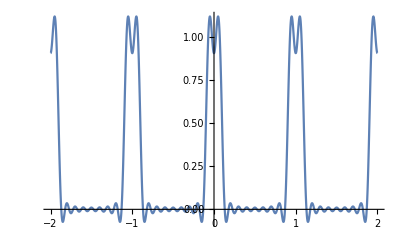

```mathematica
t = A[n] Exp[2 ⅈ π n x];
tS = Sum[t,{n,-10,-1}] +A0+ Sum[t,{n,1,10}];
Plot[tS,{x,-2,2}]
```

```mathematica
ψS =Sum[ψ1 /. An -> A[n],{n,-10,-1}]+( ψ1/. n-> 0/. An -> A0)+Sum[ψ1 /. An-> A[n],{n,1,10}]
```

233+(2 2 ψ0)/(3 k 1 λ)+(2 √(5/8+(√5)/8) ⅇ^1 ψ0)/(3 k (z+z0) λ)+(√(5/8+(√5)/8) ⅇ^((ⅈ 1)/1) ψ0)/(k (z+z0) λ)+(√(5/8+(√5)/8) ⅇ^((ⅈ (1))/(2 a^2 k (z+z0))) ψ0)/(k (z+z0) λ)+(2 √(5/8-(√5)/8) ⅇ^((ⅈ (1))/(2 a^2 k (z+z0))) ψ0)/(k (z+z0) λ)+(2 √(5/8-(√5)/8) ⅇ^((ⅈ (4 a k π x z0-4 π^2 z z0+1))/(2 a^2 k (z+z0))) ψ0)/(k (z+z0) λ)+(2 ⅇ^((ⅈ k (x^2+y^2+2 (z+z0)^2))/(2 (z+z0))) π ψ0)/(5 k (z+z0) λ)
 |  |  |  |

```mathematica
vals = {y->0, k->( 2π / λ), λ-> 10^-3,a-> 1, z0->5 10^3,ψ0-> 1};
```

```mathematica
ψS2 =Abs[ψS/. vals /. vals]^2 //Simplify
```

(ⅇ^(-10 π (10000000000-198000 x+200 x^2+3990199 z+400 z^2) Im[1/(5000+z)]) (Abs[1/(5000+z)(-140849242888308034675825876636994552640 √(10-2 √5)-140849242888308034675825876636994552640 √(10-2 √5) ⅇ^((1980000 ⅈ π x)/(5000+z))-536310578690095978188721607194710027360 √(10-2 √5) ⅇ^((45625 ⅈ π (16 x+z))/(5000+z))+13944075045942495432906761787062460711360 √(10-2 √5) ⅇ^((49000 ⅈ π (20 x+z))/(5000+z))-733898686628552391205619041424340037440 √(10-2 √5) ⅇ^((47200 ⅈ π (25 x+z))/(5000+z))-284572960121275416998097179327805320640 √(10-2 √5) ⅇ^((37000 ⅈ π (40 x+z))/(5000+z))-236340255015974498862826470967160351040 √(10-2 √5) ⅇ^((31600 ⅈ π (50 x+z))/(5000+z))+188433446566790478823064348473817036640 √(10-2 √5) ⅇ^((21625 ⅈ π (80 x+z))/(5000+z))-176507279062563233327933693507119755840 √(10-2 √5) ⅇ^((17800 ⅈ π (100 x+z))/(5000+z))+168000904167981872685623635988704345920 √(2 (5+√5)) ⅇ^((14560 ⅈ π (125 x+z))/(5000+z))-156675000516207813852884963899578210240 √(10-2 √5) ⅇ^((9400 ⅈ π (200 x+z))/(5000+z))+153231593911455993768206173484202864960 √(10-2 √5) ⅇ^((7600 ⅈ π (250 x+z))/(5000+z))+148341223893005270562837891351728305440 √(10-2 √5) ⅇ^((4825 ⅈ π (400 x+z))/(5000+z))-143753350989097891060894451413015058880 √(2 (5+√5)) ⅇ^((1960 ⅈ π (1000 x+z))/(5000+z))-142286480060637708499048589663902660320 √(2 (5+√5)) ⅇ^((985 ⅈ π (2000 x+z))/(5000+z))+228591394195778613654209209623974765760 √(10-2 √5) ⅇ^((15200 ⅈ π (25 x+2 z))/(5000+z))-208120523073768588550847190851678518080 √(2 (5+√5)) ⅇ^((13280 ⅈ π (125 x+2 z))/(5000+z))+273413236194950890841309054648283543360 √(10-2 √5) ⅇ^((12000 ⅈ π (40 x+3 z))/(5000+z))+664003573616309306328893418431545748160 √(10-2 √5) ⅇ^((15600 ⅈ π (50 x+3 z))/(5000+z))+581003126914270643037781741127602529640 √(10-2 √5) ⅇ^((15375 ⅈ π (80 x+3 z))/(5000+z))-357540385793397318792481071463140018240 √(10-2 √5) ⅇ^((13800 ⅈ π (100 x+3 z))/(5000+z))+273413236194950890841309054648283543360 √(10-2 √5) ⅇ^((12000 ⅈ π (125 x+3 z))/(5000+z))-202088044144094136708793649087861749440 √(10-2 √5) ⅇ^((8400 ⅈ π (200 x+3 z))/(5000+z))+166000893404077326582223354607886437040 √(10-2 √5) ⅇ^((4575 ⅈ π (400 x+3 z))/(5000+z))-160276724666005694631112204448993801280 √(2 (5+√5)) ⅇ^((3720 ⅈ π (500 x+3 z))/(5000+z))+149936290816585972396846900936155491520 √(2 (5+√5)) ⅇ^((1920 ⅈ π (1000 x+3 z))/(5000+z))-145250781728567660759445435281900632410 √(10-2 √5) ⅇ^((975 ⅈ π (2000 x+3 z))/(5000+z))+4648025015314165144302253929020820237120 √(2 (5+√5)) ⅇ^((8160 ⅈ π (125 x+6 z))/(5000+z))-183474671657138097801404760356085009360 √(10-2 √5) ⅇ^((2875 ⅈ π (80 x+7 z))/(5000+z))+340099391364451108119677116757620992960 √(10-2 √5) ⅇ^((5800 ⅈ π (100 x+7 z))/(5000+z))+1072621157380191956377443214389420054720 √(2 (5+√5)) ⅇ^((6880 ⅈ π (125 x+7 z))/(5000+z))-480830173998017083893336613346981403840 √(10-2 √5) ⅇ^((6400 ⅈ π (200 x+7 z))/(5000+z))+324280815021918498439692134582847923520 √(2 (5+√5)) ⅇ^((5680 ⅈ π (250 x+7 z))/(5000+z))+217876172592851491139168152922850948615 √(10-2 √5) ⅇ^((4075 ⅈ π (400 x+7 z))/(5000+z))+196395423182288668069109320944541700160 √(10-2 √5) ⅇ^((3400 ⅈ π (500 x+7 z))/(5000+z))+151566033108070602531595236815896312080 √(2 (5+√5)) ⅇ^((955 ⅈ π (2000 x+7 z))/(5000+z))-480830173998017083893336613346981403840 √(10-2 √5) ⅇ^((5600 ⅈ π (125 x+8 z))/(5000+z))+172149074641265375714898293667437786560 √(10-2 √5) ⅇ^((1800 ⅈ π (100 x+9 z))/(5000+z))-1549341671771388381434084643006940079040 √(10-2 √5) ⅇ^((5400 ⅈ π (200 x+9 z))/(5000+z))-516447223923796127144694881002313359680 √(2 (5+√5)) ⅇ^((5040 ⅈ π (250 x+9 z))/(5000+z))+258223611961898063572347440501156679840 √(10-2 √5) ⅇ^((3825 ⅈ π (400 x+9 z))/(5000+z))+221334524538769768776297806143848582720 √(2 (5+√5)) ⅇ^((3240 ⅈ π (500 x+9 z))/(5000+z))+172149074641265375714898293667437786560 √(10-2 √5) ⅇ^((1800 ⅈ π (1000 x+9 z))/(5000+z))-181091883713538901726061841390421567680 √(2 (5+√5)) ⅇ^((1760 ⅈ π (125 x+11 z))/(5000+z))+1267643185994772312082432889732950973760 √(10-2 √5) ⅇ^((4400 ⅈ π (200 x+11 z))/(5000+z))+1267643185994772312082432889732950973760 √(10-2 √5) ⅇ^((4400 ⅈ π (250 x+11 z))/(5000+z))+316910796498693078020608222433237743440 √(10-2 √5) ⅇ^((3575 ⅈ π (400 x+11 z))/(5000+z))-181091883713538901726061841390421567680 √(2 (5+√5)) ⅇ^((1760 ⅈ π (1000 x+11 z))/(5000+z))-158455398249346539010304111216618871720 √(2 (5+√5)) ⅇ^((935 ⅈ π (2000 x+11 z))/(5000+z))+149936290816585972396846900936155491520 √(2 (5+√5)) ⅇ^((480 ⅈ π (125 x+12 z))/(5000+z))+449808872449757917190540702808466474560 √(10-2 √5) ⅇ^((3400 ⅈ π (200 x+13 z))/(5000+z))+410119854292426336261963581972425315040 √(10-2 √5) ⅇ^((3325 ⅈ π (400 x+13 z))/(5000+z))-296682447786010541125675782703456610880 √(2 (5+√5)) ⅇ^((2920 ⅈ π (500 x+13 z))/(5000+z))+191014726656746512779544682014554256320 √(2 (5+√5)) ⅇ^((1720 ⅈ π (1000 x+13 z))/(5000+z))-162140407510959249219846067291423961760 √(10-2 √5) ⅇ^((925 ⅈ π (2000 x+13 z))/(5000+z))+196395423182288668069109320944541700160 √(10-2 √5) ⅇ^((1400 ⅈ π (200 x+17 z))/(5000+z))-376866893133580957646128696947634073280 √(2 (5+√5)) ⅇ^((2480 ⅈ π (250 x+17 z))/(5000+z))+996005360424463959493340127647318622240 √(10-2 √5) ⅇ^((2825 ⅈ π (400 x+17 z))/(5000+z))+449808872449757917190540702808466474560 √(10-2 √5) ⅇ^((2600 ⅈ π (500 x+17 z))/(5000+z))+170049695682225554059838558378810496480 √(2 (5+√5)) ⅇ^((905 ⅈ π (2000 x+17 z))/(5000+z))+153231593911455993768206173484202864960 √(10-2 √5) ⅇ^((400 ⅈ π (200 x+19 z))/(5000+z))+263095755583820668545410599755895485120 √(2 (5+√5)) ⅇ^((1840 ⅈ π (250 x+19 z))/(5000+z))+3486018761485623858226690446765615177840 √(10-2 √5) ⅇ^((2575 ⅈ π (400 x+19 z))/(5000+z))+606264132432282410126380947263585248320 √(2 (5+√5)) ⅇ^((2440 ⅈ π (500 x+19 z))/(5000+z))+228591394195778613654209209623974765760 √(10-2 √5) ⅇ^((1600 ⅈ π (1000 x+19 z))/(5000+z))-202088044144094136708793649087861749440 √(10-2 √5) ⅇ^((1200 ⅈ π (250 x+21 z))/(5000+z))-2324012507657082572151126964510410118560 √(10-2 √5) ⅇ^((2325 ⅈ π (400 x+21 z))/(5000+z))-244632895542850797068539680474780012480 √(2 (5+√5)) ⅇ^((1560 ⅈ π (1000 x+21 z))/(5000+z))-178770192896698659396240535731570009120 √(2 (5+√5)) ⅇ^((885 ⅈ π (2000 x+21 z))/(5000+z))-871504690371405964556672611691403794460 √(10-2 √5) ⅇ^((2075 ⅈ π (400 x+23 z))/(5000+z))-1992010720848927918986680255294637244480 √(2 (5+√5)) ⅇ^((2120 ⅈ π (500 x+23 z))/(5000+z))+263095755583820668545410599755895485120 √(2 (5+√5)) ⅇ^((1520 ⅈ π (1000 x+23 z))/(5000+z))-183474671657138097801404760356085009360 √(10-2 √5) ⅇ^((875 ⅈ π (2000 x+23 z))/(5000+z))-387335417942847095358521160751735019760 √(10-2 √5) ⅇ^((1575 ⅈ π (400 x+27 z))/(5000+z))-1549341671771388381434084643006940079040 √(10-2 √5) ⅇ^((1800 ⅈ π (500 x+27 z))/(5000+z))+193667708971423547679260580375867509880 √(2 (5+√5)) ⅇ^((855 ⅈ π (2000 x+27 z))/(5000+z))-303132066216141205063190473631792624160 √(10-2 √5) ⅇ^((1325 ⅈ π (400 x+29 z))/(5000+z))-820239708584852672523927163944850630080 √(2 (5+√5)) ⅇ^((1640 ⅈ π (500 x+29 z))/(5000+z))+340099391364451108119677116757620992960 √(10-2 √5) ⅇ^((1400 ⅈ π (1000 x+29 z))/(5000+z))-249001340106115989873335031911829655560 √(10-2 √5) ⅇ^((1075 ⅈ π (400 x+31 z))/(5000+z))-376866893133580957646128696947634073280 √(2 (5+√5)) ⅇ^((1360 ⅈ π (1000 x+31 z))/(5000+z))-205059927146213168130981790986212657520 √(2 (5+√5)) ⅇ^((835 ⅈ π (2000 x+31 z))/(5000+z))-211273864332462052013738814955491828960 √(10-2 √5) ⅇ^((825 ⅈ π (400 x+33 z))/(5000+z))+422547728664924104027477629910983657920 √(2 (5+√5)) ⅇ^((1320 ⅈ π (500 x+33 z))/(5000+z))+422547728664924104027477629910983657920 √(2 (5+√5)) ⅇ^((1320 ⅈ π (1000 x+33 z))/(5000+z))-211273864332462052013738814955491828960 √(10-2 √5) ⅇ^((825 ⅈ π (2000 x+33 z))/(5000+z))-162140407510959249219846067291423961760 √(10-2 √5) ⅇ^((325 ⅈ π (400 x+37 z))/(5000+z))-284572960121275416998097179327805320640 √(10-2 √5) ⅇ^((1000 ⅈ π (500 x+37 z))/(5000+z))+224904436224878958595270351404233237280 √(2 (5+√5)) ⅇ^((805 ⅈ π (2000 x+37 z))/(5000+z))-145250781728567660759445435281900632410 √(10-2 √5) ⅇ^((75 ⅈ π (400 x+39 z))/(5000+z))-244632895542850797068539680474780012480 √(2 (5+√5)) ⅇ^((840 ⅈ π (500 x+39 z))/(5000+z))+664003573616309306328893418431545748160 √(10-2 √5) ⅇ^((1200 ⅈ π (1000 x+39 z))/(5000+z))-820239708584852672523927163944850630080 √(2 (5+√5)) ⅇ^((1160 ⅈ π (1000 x+41 z))/(5000+z))-240415086999008541946668306673490701920 √(2 (5+√5)) ⅇ^((785 ⅈ π (2000 x+41 z))/(5000+z))+191014726656746512779544682014554256320 √(2 (5+√5)) ⅇ^((520 ⅈ π (500 x+43 z))/(5000+z))+1072621157380191956377443214389420054720 √(2 (5+√5)) ⅇ^((1120 ⅈ π (1000 x+43 z))/(5000+z))-249001340106115989873335031911829655560 √(10-2 √5) ⅇ^((775 ⅈ π (2000 x+43 z))/(5000+z))-156675000516207813852884963899578210240 √(10-2 √5) ⅇ^((200 ⅈ π (500 x+47 z))/(5000+z))+268155289345047989094360803597355013680 √(2 (5+√5)) ⅇ^((755 ⅈ π (2000 x+47 z))/(5000+z))-143753350989097891060894451413015058880 √(2 (5+√5)) ⅇ^((40 ⅈ π (500 x+49 z))/(5000+z))+13944075045942495432906761787062460711360 √(10-2 √5) ⅇ^((1000 ⅈ π (1000 x+49 z))/(5000+z))+4648025015314165144302253929020820237120 √(2 (5+√5)) ⅇ^((960 ⅈ π (1000 x+51 z))/(5000+z))-290501563457135321518890870563801264820 √(2 (5+√5)) ⅇ^((735 ⅈ π (2000 x+51 z))/(5000+z))-1992010720848927918986680255294637244480 √(2 (5+√5)) ⅇ^((920 ⅈ π (1000 x+53 z))/(5000+z))-303132066216141205063190473631792624160 √(10-2 √5) ⅇ^((725 ⅈ π (2000 x+53 z))/(5000+z))+332001786808154653164446709215772874080 √(2 (5+√5)) ⅇ^((705 ⅈ π (2000 x+57 z))/(5000+z))-733898686628552391205619041424340037440 √(10-2 √5) ⅇ^((800 ⅈ π (1000 x+59 z))/(5000+z))+606264132432282410126380947263585248320 √(2 (5+√5)) ⅇ^((760 ⅈ π (1000 x+61 z))/(5000+z))-366949343314276195602809520712170018720 √(2 (5+√5)) ⅇ^((685 ⅈ π (2000 x+61 z))/(5000+z))-516447223923796127144694881002313359680 √(2 (5+√5)) ⅇ^((720 ⅈ π (1000 x+63 z))/(5000+z))-387335417942847095358521160751735019760 √(10-2 √5) ⅇ^((675 ⅈ π (2000 x+63 z))/(5000+z))+435752345185702982278336305845701897230 √(2 (5+√5)) ⅇ^((655 ⅈ π (2000 x+67 z))/(5000+z))-357540385793397318792481071463140018240 √(10-2 √5) ⅇ^((600 ⅈ π (1000 x+69 z))/(5000+z))+324280815021918498439692134582847923520 √(2 (5+√5)) ⅇ^((560 ⅈ π (1000 x+71 z))/(5000+z))-498002680212231979746670063823659311120 √(2 (5+√5)) ⅇ^((635 ⅈ π (2000 x+71 z))/(5000+z))-296682447786010541125675782703456610880 √(2 (5+√5)) ⅇ^((520 ⅈ π (1000 x+73 z))/(5000+z))-536310578690095978188721607194710027360 √(10-2 √5) ⅇ^((625 ⅈ π (2000 x+73 z))/(5000+z))+633821592997386156041216444866475486880 √(2 (5+√5)) ⅇ^((605 ⅈ π (2000 x+77 z))/(5000+z))-236340255015974498862826470967160351040 √(10-2 √5) ⅇ^((400 ⅈ π (1000 x+79 z))/(5000+z))+221334524538769768776297806143848582720 √(2 (5+√5)) ⅇ^((360 ⅈ π (1000 x+81 z))/(5000+z))-774670835885694190717042321503470039520 √(2 (5+√5)) ⅇ^((585 ⅈ π (2000 x+81 z))/(5000+z))-208120523073768588550847190851678518080 √(2 (5+√5)) ⅇ^((320 ⅈ π (1000 x+83 z))/(5000+z))-871504690371405964556672611691403794460 √(10-2 √5) ⅇ^((575 ⅈ π (2000 x+83 z))/(5000+z))+1162006253828541286075563482255205059280 √(2 (5+√5)) ⅇ^((555 ⅈ π (2000 x+87 z))/(5000+z))-176507279062563233327933693507119755840 √(10-2 √5) ⅇ^((200 ⅈ π (1000 x+89 z))/(5000+z))+168000904167981872685623635988704345920 √(2 (5+√5)) ⅇ^((160 ⅈ π (1000 x+91 z))/(5000+z))-1743009380742811929113345223382807588920 √(2 (5+√5)) ⅇ^((535 ⅈ π (2000 x+91 z))/(5000+z))-160276724666005694631112204448993801280 √(2 (5+√5)) ⅇ^((120 ⅈ π (1000 x+93 z))/(5000+z))-2324012507657082572151126964510410118560 √(10-2 √5) ⅇ^((525 ⅈ π (2000 x+93 z))/(5000+z))+6972037522971247716453380893531230355680 √(2 (5+√5)) ⅇ^((505 ⅈ π (2000 x+97 z))/(5000+z))+6972037522971247716453380893531230355680 √(2 (5+√5)) ⅇ^((485 ⅈ π (2000 x+101 z))/(5000+z))+3486018761485623858226690446765615177840 √(10-2 √5) ⅇ^((475 ⅈ π (2000 x+103 z))/(5000+z))-1743009380742811929113345223382807588920 √(2 (5+√5)) ⅇ^((455 ⅈ π (2000 x+107 z))/(5000+z))+1162006253828541286075563482255205059280 √(2 (5+√5)) ⅇ^((435 ⅈ π (2000 x+111 z))/(5000+z))+996005360424463959493340127647318622240 √(10-2 √5) ⅇ^((425 ⅈ π (2000 x+113 z))/(5000+z))-774670835885694190717042321503470039520 √(2 (5+√5)) ⅇ^((405 ⅈ π (2000 x+117 z))/(5000+z))+633821592997386156041216444866475486880 √(2 (5+√5)) ⅇ^((385 ⅈ π (2000 x+121 z))/(5000+z))+581003126914270643037781741127602529640 √(10-2 √5) ⅇ^((375 ⅈ π (2000 x+123 z))/(5000+z))-498002680212231979746670063823659311120 √(2 (5+√5)) ⅇ^((355 ⅈ π (2000 x+127 z))/(5000+z))+435752345185702982278336305845701897230 √(2 (5+√5)) ⅇ^((335 ⅈ π (2000 x+131 z))/(5000+z))+410119854292426336261963581972425315040 √(10-2 √5) ⅇ^((325 ⅈ π (2000 x+133 z))/(5000+z))-366949343314276195602809520712170018720 √(2 (5+√5)) ⅇ^((305 ⅈ π (2000 x+137 z))/(5000+z))+332001786808154653164446709215772874080 √(2 (5+√5)) ⅇ^((285 ⅈ π (2000 x+141 z))/(5000+z))+316910796498693078020608222433237743440 √(10-2 √5) ⅇ^((275 ⅈ π (2000 x+143 z))/(5000+z))-290501563457135321518890870563801264820 √(2 (5+√5)) ⅇ^((255 ⅈ π (2000 x+147 z))/(5000+z))+268155289345047989094360803597355013680 √(2 (5+√5)) ⅇ^((235 ⅈ π (2000 x+151 z))/(5000+z))+258223611961898063572347440501156679840 √(10-2 √5) ⅇ^((225 ⅈ π (2000 x+153 z))/(5000+z))-240415086999008541946668306673490701920 √(2 (5+√5)) ⅇ^((205 ⅈ π (2000 x+157 z))/(5000+z))+224904436224878958595270351404233237280 √(2 (5+√5)) ⅇ^((185 ⅈ π (2000 x+161 z))/(5000+z))+217876172592851491139168152922850948615 √(10-2 √5) ⅇ^((175 ⅈ π (2000 x+163 z))/(5000+z))-205059927146213168130981790986212657520 √(2 (5+√5)) ⅇ^((155 ⅈ π (2000 x+167 z))/(5000+z))+193667708971423547679260580375867509880 √(2 (5+√5)) ⅇ^((135 ⅈ π (2000 x+171 z))/(5000+z))+188433446566790478823064348473817036640 √(10-2 √5) ⅇ^((125 ⅈ π (2000 x+173 z))/(5000+z))-178770192896698659396240535731570009120 √(2 (5+√5)) ⅇ^((105 ⅈ π (2000 x+177 z))/(5000+z))+170049695682225554059838558378810496480 √(2 (5+√5)) ⅇ^((85 ⅈ π (2000 x+181 z))/(5000+z))+166000893404077326582223354607886437040 √(10-2 √5) ⅇ^((75 ⅈ π (2000 x+183 z))/(5000+z))-158455398249346539010304111216618871720 √(2 (5+√5)) ⅇ^((55 ⅈ π (2000 x+187 z))/(5000+z))+151566033108070602531595236815896312080 √(2 (5+√5)) ⅇ^((35 ⅈ π (2000 x+191 z))/(5000+z))+148341223893005270562837891351728305440 √(10-2 √5) ⅇ^((25 ⅈ π (2000 x+193 z))/(5000+z))-142286480060637708499048589663902660320 √(2 (5+√5)) ⅇ^((5 ⅈ π (2000 x+197 z))/(5000+z))+11155260036753996346325409429649968569088 ⅇ^((495 ⅈ π (2000 x+99 z))/(5000+z)) π)])^2)/(3110995662190019297886905525352394061318321868786387973704705135057657555728793600 π^2)

```mathematica
DensityPlot[ψS2,{x,-1,1},{z,0,4000},PlotPoints->2000,ColorFunction->"Rainbow",PlotRange->Full]
```

-Graphics-

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}